```mathematica
200 2 π/0.02
```

2

```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
ω1=0.2;
ω2=0.2/30;
ω3=-0.002;
angle =0.0;
anitropy=0;
B[{ω1_,ω2_,ω3_,angle_},t_,ind_]:={  Sin[  ω1 t] Sin[ ω2   t]*0 ,Sin[ ω1 t] +0*Cos[  ω2 t]  ,Cos[ω1 t ]   }.RotationMatrix[angle Degree*Boole[ind] ,{0,1,0}];

roller[ω1_,ω2_,ω3_,angle_,field_]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol


},
parameter={ω1,ω2,ω3,angle};
tMax = Min[200 2 π/parameter[[1]],50000.0];
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t ,field[[1]]     ]   ]];
(*force *)
F ={Sin[parameter[[4]] Degree] *anitropy*Boole[field[[2]]] ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π]*0,θ->RandomReal[2 π]*0,ψ->RandomReal[2 π]*0};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
]
```

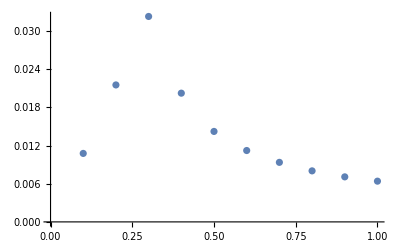

```mathematica
ListPlot[Table[{i,roller[i,ω2,ω3,angle,{True,False}]},{i,0.1,1,0.1}]]
```

```mathematica
RollVelocity=Table[{i,roller[i,ω2,ω3,angle,{True,False}]},{i,0.001,1,0.001}];
```

```mathematica
roller[10^-6,ω2,ω3,angle,{True,False}]
```

1.07724×10^-7

9.28296

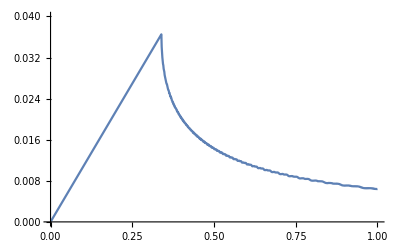

```mathematica
ListPlot[RollVelocity,Joined->True,PlotRange->{{0,1},{0,0.04}}]
```

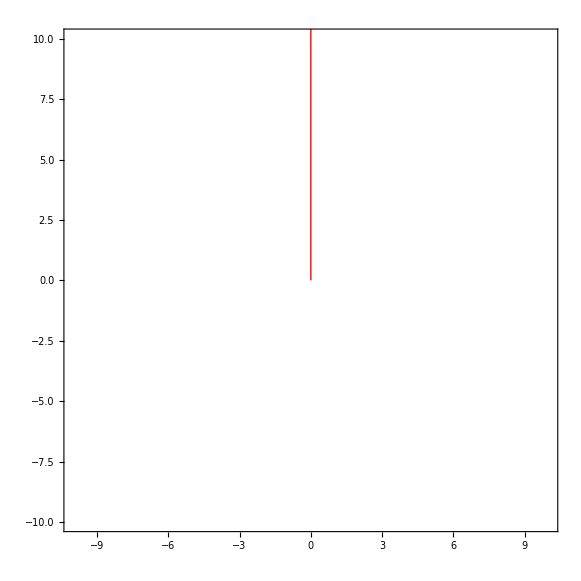

```mathematica
ParametricPlot[{x[t]/.sol[[1]],y[t]/.sol[[1]]},{t,0,6000},PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red, Thick},Frame->True,Axes->False]
```